# PH 427 Homework 10 -- John Waczak

5. Calculate the probability that the electron is in the classically forbidden region for the n=2 states of hydrogen. Discuss the differences between the results for ℓ=0 and ℓ=1. 

In order to define the classically forbidden region, we need to consider the quantum version of the Effective Potential. (I am using SI units)

```mathematica
Z = 1
ϵ0 = 8.854*10^(-12) 
V[r_]:= -e^2/(4*π*ϵ0*r)
Subscript[m, e]=9.1*10^(-31)
Subscript[m, p] = 1.7*10^(-27)
μ=(Subscript[m, e]*Subscript[m, p])/(Subscript[m, e]+Subscript[m, p])
Subscript[V, eff][r_,ℓ_]=((ℏ^2*ℓ*(ℓ+1))/(2*μ*r^2)+V[r])
a0 = 5.29*10^-11
```

The following plot shows V_eff(r) for ℓ values 0,1, and 2

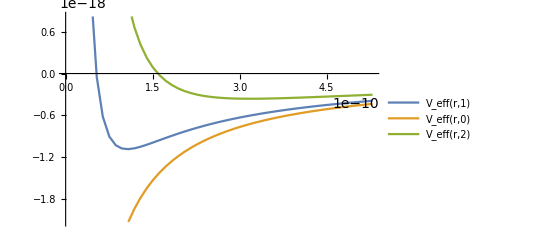

```mathematica
Plot[{Subscript[V, eff][r,1],Subscript[V, eff][r,0],Subscript[V, eff][r,2]},{r,0,10*a0}, PlotLegends->"Expressions"]
```

Now we know that for our states, n=2 which means that the total energy is (-13.6 eV)/2^2which we can use to solve for the bounds of the classically forbidden region. To do this we observe that -13.6/v eV = -5.44*10^-19 Joules

-5.4468×10^-19

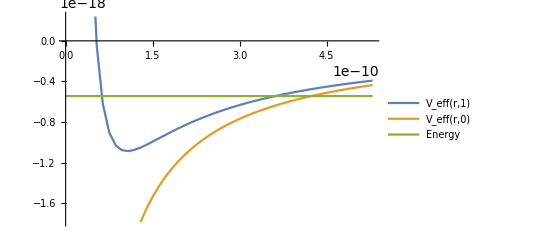

```mathematica
Energy= (-13.6/4)*e 
Plot[{Subscript[V, eff][r,1],Subscript[V, eff][r,0],Energy},{r,0,10*a0}, PlotLegends->"Expressions"]
```

```mathematica
Solve[Subscript[V, eff][r,0]==Energy, r]
```

{{r→4.23481×10^-10}}

```mathematica
Solve[Subscript[V, eff][r,1]==Energy, r]
```

{{r→6.21234×10^-11},{r→3.61358×10^-10}}

```mathematica
r1 = 4.23481*^-10
r2 = 6.21234*^-11
r3 = 3.61358*^-10
```

4.23481×10^-10

6.21234×10^-11

3.61358×10^-10

Now we have that the classical region for ℓ=0 is [0,r1] and for ℓ=1 is [r2, r3]. We can now use this information to evaluate the probability that a particular eigenstate |n,ℓ,m⟩ is in the classical region. Then 1-P will give the probability that we can find the particle in the classically forbidden region. I have chosen to do this as I’d imagine integrating outside of those bounds will be more difficult as it will involve ∞. There are 4 possible states for n=2: |2,0,0⟩ which corresponds to ℓ=0 and |2,1,-1⟩, |2,1,0⟩, |2,1,-1⟩ which correspond to ℓ=1.

```mathematica
Subscript[ψ, 200][r_,θ_,ϕ_]:=1/(√π)*(Z/(2*a0))^(3/2)*(1-(Z*r)/(2*a0))*Exp[(-Z*r)/(2*a0)]
Subscript[ψ, 210][r_,θ_,ϕ_]:= 1/(2*√π)*(Z/(2*a0))^(3/2)*(Z*r)/a0*Exp[(-Z*r)/(2*a0)]*Cos[θ]
```

```mathematica
Subscript[ψ, 211][r_,θ_,ϕ_]:= -1/(2*√(2π))*(Z/(2*a0))^(3/2)*(Z*r)/a0*Exp[(-Z*r)/(2*a0)]*Sin[θ]*Exp[ⅈ*ϕ]
Subscript[ψ, 21-1][r_,θ_,ϕ_]:= 1/(2*√(2π))*(Z/(2*a0))^(3/2)*(Z*r)/a0*Exp[(-Z*r)/(2*a0)]*Sin[θ]*Exp[-ⅈ*ϕ]
```

We now find the probabilities for being within the classically allowed region

```mathematica
Integrate[Conjugate[Subscript[ψ, 200][r,θ,ϕ]]*Subscript[ψ, 200][r,θ,ϕ]*r^2*Sin[θ],{r,0,r1},{θ,0,π},{ϕ,0,2*π}]
```

0.815002

```mathematica
Integrate[Conjugate[Subscript[ψ, 210][r,θ,ϕ]]*Subscript[ψ, 210][r,θ,ϕ]*r^2*Sin[θ],{r,r2,r3},{θ,0,π},{ϕ,0,2*π}]
```

0.803924

```mathematica
Integrate[Conjugate[Subscript[ψ, 21-1][r,θ,ϕ]]*Subscript[ψ, 21-1][r,θ,ϕ]*r^2*Sin[θ],{r,r2,r3},{θ,0,π},{ϕ,0,2*π}]
```

0.803924

```mathematica
Integrate[Conjugate[Subscript[ψ, 211][r,θ,ϕ]]*Subscript[ψ, 211][r,θ,ϕ]*r^2*Sin[θ],{r,r2,r3},{θ,0,π},{ϕ,0,2*π}]
```

0.803924

```mathematica
Subscript[P, 200] = 1-0.815002
Subscript[P, 210] = 1-0.803924
Subscript[P, 21-1]= 1-0.803924
Subscript[P, 211]=1- 0.803924
```

0.184998

0.196076

0.196076

0.196076

As we can see from above, the probabilities are nearly the same for the ℓ = 0 and ℓ = 1 states.